# Lecture Notes

## Lecture 1-2

#### What is this course?

只介绍核心语言

从 2+2=4 到MMA中没有的运算

没有实用型内容

不关心数据结构、算法

#### Why we need programming?

理论建设者

问题求解者：need a lot of calculation

把机器的工作交给机器，把人的工作留给人

根据可计算性理论，人能计算的东西机器都能计算

## Lecture 1-3

#### Key point

充分理解我们所做的计算，将它归结为“重写规则”

将“重写规则”教给计算机，使它可以帮助我们完成计算

为了方便表达“重写规则”，我们需要一种合适的语言

Mathematica 的核心语言是一种很好的选择

#### 作为计算器的 Mathematica

```mathematica
2+2;
```

```mathematica
FactorInteger[2^(2^5)+1];
```

```mathematica
FactorInteger[2^2^5+1];
```

```mathematica
N[EulerGamma,20];
```

```mathematica
Expand[(a + b)^3];
```

```mathematica
Factor[x^3 + y^3 + z^3 - 3 x y z];(*xyz 之间有空格，表示是变量相乘*)
```

```mathematica
Sum[x^(2n)/(n^2 Binomial[2n,n]),{n,1,Infinity}];
```

```mathematica
FullSimplify[DSolve[{y''[x]+y[x]==8x Sin[x],y[0]==0,y'[0]==0},y[x],x]];
```

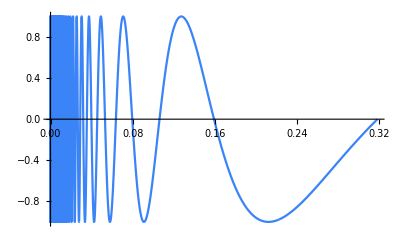

```mathematica
Plot[Sin[1/x],{x,0,1/Pi},PlotPoints->10000]
```

## Lecture 1-4

#### Mathematica 的两部分

前端

内核

#### Some interesting functions:

Sound

Import: 能直接从网上抓图和处理图片

FindFaces: 人脸识别

FinancialData: 抓取实时股票价格

Classify: 机器学习

#### Mathematica 有一些很高级的函数，适用于快速实现一些复杂程序，即便效率可能不够高

### 接下来讲核心语言

#### 值、变量、类型

以下三种对象称为原子（atom）：无法再分的表达式

符号 Symbol：字母和数字（数字不能在起始位置）构成的有限序列

数字 Number：整数、有理数、实数、复数

字符串 String：双引号“”括起来的任意字符构成的有限序列

符号可以认为是变量，数字和字符串则是变量的值

系统有一些内建符号

开头字母大写的单词（Camel 命名法）

用来做判断的函数末尾通常有“Q”

建议采取 camel 命名法，首字母小写

变量名建议使用有意义的单词，长一些没问题，有自动补全

```mathematica
张三欠的钱=2000元;
李四欠的钱=30000元;
加=Plus;
张三和李四一共欠的钱=张三欠的钱~加~李四欠的钱
```

32000 元

## Lecture 1-5

在上面的例子里，“~” 是函数的中缀

#### 类型检查问题

```mathematica
Plot[Sin[x],{x,"0",2Pi}](*通不过检查*)
Sin["string"]
Sin["string"]/.{"string"->0}
```

Plot::plln: Limiting value 0 in {x,0,2 π} is not a machine-sized real number.

Plot[Sin[x],{x,0,2 π}]

Sin[string]

0

#### 条件、循环、子程序

条件结构的功能可以通过模式匹配来完成

循环结构的功能可以通过表处理和泛函编程来完成

#### 简单条件判断

```mathematica
If[a==b,Print["True"],Print["False"],Print["Unevaluated"]]
```

Unevaluated

```mathematica
If[a === b, Print["True"], Print["False"], Print["Unevaluated"]]
```

False

#### 多重条件判断

```mathematica
x=1;
Which[x==1,1,x==2,2,x==3,3,True,Print["x!=1,2,3"]](*逐个条件检验，如果某步无法判断则不输出*)
```

1

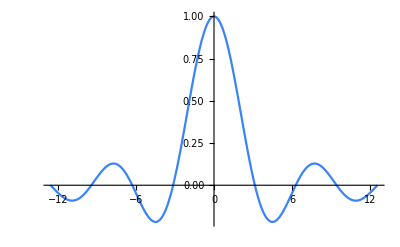

```mathematica
Plot[Piecewise[{{1,x==0},{Sin[x]/x,x!=0}}],{x,-4Pi,4Pi}]
```

```mathematica
Switch[b,True,1,False,0,_,Print["b is not a boolean value."]](*比较复杂，先不讲*)
```

b is not a boolean value.

#### 简单循环

```mathematica
Do[Print["yoo, "],{2}];Print["check it out! "]
```

yoo,

yoo,

check it out!

```mathematica
Do[Print[Prime[i]],{i,PrimePi[20]}]
```

```mathematica
Do[Print[i], {i, 1, 5}](*5是包含的*)
```

```mathematica
Do[Print[i," is a prime number."],{i,{2,3,5,7}}]
```

2 is a prime number.

3 is a prime number.

5 is a prime number.

7 is a prime number.

#### 复杂循环

```mathematica
For[i=1;t=i,i<=6,i++,Print[t*=i]](*用逗号隔开：初始值、条件判断、循环变量的迭代、每步循环的操作*)
```

1

2

6

24

120

720

```mathematica
n=1234567;While[Not[PrimeQ[++n]]];n(*n++和++n是不一样的*)
```

1234577

```mathematica
n=1234567;Catch[Do[If[PrimeQ[i],Throw[i]],{i,n,2n}]](*用于抛出异常，catch成功一次后停止*)
```

不推荐使用：Break, Continue, Return, Goto。

#### 函数定义方法

模式匹配+延迟赋值

```mathematica
f[x_]:=x^2;
```

```mathematica
f[x_,y_]:=x y;
```

纯函数（λ表达式、匿名函数）

```mathematica
f1=Function[x,x^2];(*完整形式*)
```

```mathematica
f2=#^2&;(*简写形式*)
```

```mathematica
g1=Function[{x,y},x y];
g2=#1 #2 &;
```

推荐初学者使用方法二的完整形式

#### 例子：求不大于给定正整数 n 的所有素数的和

```mathematica
(*类C实现*)
myPrimeQ = Function[x,i=2;max=Floor[Sqrt[x]]+1;While[Mod[x,i]!=0&&i<max,i++];i>=max];(*当i模 x=0 或者 i>=max 时，才会跳出 While 循环，如果跳出循环的是 i>=max, 那么说明找不到因数，x是素数*)
```

```mathematica
myPrimeSum=Function[n,
sum=0;
Do[If[myPrimeQ[x],sum+=x],{x,2,n}];
sum];
```

```mathematica
(*核心语言实现*)(*快是因为 MMA 存了前 10 亿个素数表*)
myPrimeSum2=Plus@@Prime/@Range@PrimePi[#]&;
myPrimeSum2=Function[n,Apply[Plus, Map[Prime, Range[PrimePi[n]]]]];(*上面那行的特殊符号的翻译*)
```

```mathematica
Timing[#[100000]]&/@{myPrimeSum,myPrimeSum2}(*比较运行时间*)
```

{{3.05356,454396537},{0.048714,454396537}}

## Lecture 2-1

#### Mathematica 核心语言和 C 的本质区别在于范式

C 是命令式的，面向过程的；MMA是函数式的

Wolfram 是如何写出 MMA 的：

```mathematica
http://www.wolfram.com/mathematica/scrapbook
```

## Lecture 2-2

#### Lisp: 第二古老的高级程序语言

表处理：(item1(item2(item3)item4))
(函数名 自变量1 自变量2 ...)

#### 在MMA里可以用 TreeForm 来获得表达式的语法树

```mathematica
TreeForm[(a+b^n)/z==x];
FullForm[(a+b^n)/z==x];
TraditionalForm[(a+b^n)/z==x];
(*** 写成Lisp的形式 (=(*(+a(expt b n))(expt z -1))x) ***)
(** MMA 里只有加法和乘法，没有除法和减法 **)
```

MMA 是这样来理解表达式的：函数名[参数1, 参数2]

#### 表达式的递归定义

原子对象是表达式；

若F，X1，X2... Xn 是表达式，则 F[X1, X2...Xn] 也是表达式；

MMA 中一切对象都是表达式，一个 MMA 程序就是一个表达式。

#### Mathematica 的第一原理：所有对象都是表达式

#### Mathematica 的第二原理：计算即重写

```mathematica
Trace[(#2-#1)&@@(Integrate[Sin[x]^2,x]/.{x->#}&/@{0,2Pi})]
```

{{(∫Sin[x]^2 ⅆx/.{x→#1}&)/@{0,2 π},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π]},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],∫Sin[x]^2 ⅆx/.{x→0},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→0,x→0},{x→0}},x/2-1/4 Sin[2 x]/.{x→0},0/2-1/4 Sin[2 0],{0/2,0},{{{2 0,0},Sin[0],0},-0/4,0},0+0,0},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π],∫Sin[x]^2 ⅆx/.{x→2 π},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→2 π,x→2 π},{x→2 π}},x/2-1/4 Sin[2 x]/.{x→2 π},(2 π)/2-1/4 Sin[2 (2 π)],{(2 π)/2,(2 π)/2,π},{{{2 (2 π),2 2 π,4 π},Sin[4 π],0},-0/4,0},π+0,π},{0,π}},(#2-#1&)@@{0,π},(#2-#1&)[0,π],π-0,{-0,0},π+0,π}

#### 仔细分析发现，每一步里我们都在做两件事：

从待计算对象中识别一些可化简的模式（模式匹配）

将识别出的模式用已知的规则进行化简（规则代入）

基于模式和规则的计算模型在数理逻辑/计算机科学里叫作重写系统（rewriting system）

## Lecture 2-3

F[x] 的函数头 F 也是表达式

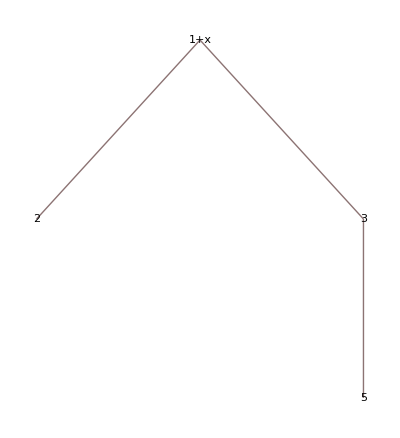

```mathematica
TreeForm[(1+x)[2,3[5]],6]
```

#### Mathematica 的第零原理：重要的是函数，而非变量

尽可能对函数进行操作，而不要对数值进行操作

#### MMA 核心语言主要内容：表达式、重写系统、函数式编程和模块化

#### 表达式与表

F[x1,x2,...] 其中 F 是函数的头（Head）

```mathematica
Head/@{1,1/2,True,"Number",a+b,a-b,(f1+f2)[x1,x2,x3]}(*跳过了{}对应的 list 结构*)
```

{Integer,Rational,Symbol,String,Plus,Plus,f1+f2}

/@ 的全名叫 Map，可以方便地测试一个函数在一组变量上的作用效果，而不必把函数头写很多遍

```mathematica
h/@k[x1,x2,x3](*跳过了 k 这个函数*)
```

k[h[x1],h[x2],h[x3]]

判断一个表达式是否是原子

```mathematica
myAtomQ=
Function[ex,
MemberQ[{Symbol, Integer, Rational, Reals,Complex, String,Image},
Head[ex]]];
```

我们也需要将表达式的参数部分取出来，它们是一些表达式构成的序列，是没有头的。但在MMA里所有表达式都有头，所以我们规定所有无头表达式的头都是 List

把身体取出来/换头:

```mathematica
ex=f[x1,x2,x3];
List@@ex
Apply[List,ex]
```

{x1,x2,x3}

{x1,x2,x3}

## Lecture 2-4

表这种表达式还有一种变体叫序列（Sequence），序列可以认为是没有{}的表

```mathematica
ex=h[1,2,3];
seq=Sequence@@ex;
lst=List@@ex;
g[seq]
g[lst]
g[seq,lst,4,5,6]
```

g[1,2,3]

g[{1,2,3}]

g[1,2,3,{1,2,3},4,5,6]

上面例子说明，当我们想把一个表达式的参数传给另一个函数时，用List 换头可能不是我们想要的，因为多了一层{}，所以会用到 Sequence

除了 Head 和 Apply，MMA 还有一种访问符和表达式内部表达式的方法，即内建函数 Part，简写为[[...]]

```mathematica
ex=g[x1,x2,x3];
{ex[[0]],ex[[1]],ex[[2]],ex[[3]],ex[[4]]}
```

Part::partw: Part 4 of g[x1,x2,x3] does not exist.

{g,x1,x2,x3,g[x1,x2,x3]⟦4⟧}

```mathematica
ex=g[a,b,h[c,k[d,e]]];
ex[[3]][[2]][[2]];
ex[[3,2,2]];
Part[ex,3,2,2];
```

```mathematica
ex=Range[1,10];
ex[[{2,3,5}]]
ex[[1;;6]](*;;表示区间*)
ex[[1;;8;;2]](*表示步长*)
```

{2,3,5}

{1,2,3,4,5,6}

{1,3,5,7}

```mathematica
Function[op,op[g[x1,x2,x3,x4]]]/@{First,Last,Rest,Most}
```

{x1,x4,g[x2,x3,x4],g[x1,x2,x3]}

```mathematica
Take[g[x1,x2,x3,x4],{2,4}](*{}表示2到4*)
Drop[g[x1,x2,x3,x4],{2,4}]
```

g[x2,x3,x4]

g[x1]

g[a,b,h[c,k[d,e]]]

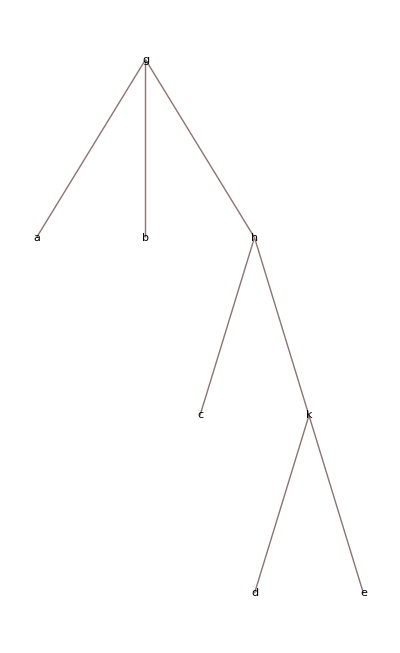

3

4

```mathematica
ex=g[a,b,h[c,k[d,e]]]
TreeForm[ex]
Length[ex](*树的第一层有多少个atom*)
Depth[ex](*树有多少层*)
```

## Lecture 2-5

#### 表的构造：

```mathematica
Range[2,10,3]
Table[i^2+i+1,{i,0,10}](*默认从1开始*)
MatrixForm[Table[KroneckerDelta[i,j-1]+t KroneckerDelta[i,j+4],{i,5},{j,5}]]
```

{2,5,8}

{1,3,7,13,21,31,43,57,73,91,111}

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
t | 0 | 0 | 0 | 0)

```mathematica
Array[#^2+#+1&,10](*匿名函数*)
```

```mathematica
Array[f,5,2,h](*5表示长度；2表示初始值；h是指定的函数头，默认是List*)
```

h[f[2],f[3],f[4],f[5],f[6]]

```mathematica
Tuples[Range[3],2](*给出所有有序元组*)
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
Outer[f,Range[3],Range[2]]//MatrixForm
```

(f[1,1] | f[1,2]
f[2,1] | f[2,2]
f[3,1] | f[3,2])

#### 查询和搜索

```mathematica
ex=f[x1,x2,x3,x4];
Function[i,MemberQ[ex,i]]/@{f,x1,x2,x3,x4,x5}(*函数头不算成员*)
Function[i,FreeQ[ex,i]]/@{f,x1,x2,x3,x4,x5}(*是否不存在某元素*)
```

{False,True,True,True,True,False}

{False,False,False,False,False,True}

```mathematica
MemberQ[ex,f,Heads->True](*参数设置*)
FreeQ[{{1,3,0},{2,1,2}},0]
FreeQ[{{1,3,0},{2,1,2}},0,1](*末位1是指定搜索深度*)
```

True

False

True

```mathematica
euler=(a+b^n)/n==x;
{Count[euler,n],Count[euler,n,Infinity]}(*默认深度是1*)
```

{0,2}

```mathematica
Position[euler,n]
```

{{1,1,2,2},{1,2,1}}

#### 挑选

```mathematica
Select[Prime/@Range[10],OddQ](*从前十个素数里找奇数*)
Select[Prime/@Range[10],Mod[#,4]==1&]
```

{3,5,7,11,13,17,19,23,29}

{5,13,17,29}

#### 添加、删除和修改

```mathematica
ex=f[a,b,c];
{Prepend[ex,z],Append[ex,d],Insert[ex,i,2],Insert[ex,i,-2],ex}(*不改变原表达式*)
```

{f[z,a,b,c],f[a,b,c,d],f[a,i,b,c],f[a,b,i,c],f[a,b,c]}

```mathematica
{PrependTo[ex,z],AppendTo[ex,d],ex}(*改变原表达式*)
```

{f[z,a,b,c],f[z,a,b,c,d],f[z,a,b,c,d]}

AppendTo 这个函数比较慢，尽量不用

```mathematica
{ex,Delete[ex,1],Delete[ex,{{1},{-1}}]}
```

{f[z,a,b,c,d],f[a,b,c,d],f[a,b,c]}

```mathematica
{ex,ReplacePart[ex,1->x]}
```

{f[z,a,b,c,d],f[x,a,b,c,d]}

```mathematica
ex[[1]]=y;
ex
```

f[y,a,b,c,d]

```mathematica
{ex,Reverse[ex],RotateLeft[ex],RotateRight[ex]}
```

{f[y,a,b,c,d],f[d,c,b,a,y],f[a,b,c,d,y],f[d,y,a,b,c]}

头部一样的表达式之间的集合运算

```mathematica
Join[f[x1,x2],f[x1,x3]]
```

f[x1,x2,x1,x3]

```mathematica
Union[f[x1,x2],f[x1,x3]]
Union[{1,2,3,2,4,3,5,7,0}]
```

f[x1,x2,x3]

{0,1,2,3,4,5,7}

```mathematica
Intersection[f[x1,x2],f[x1,x3]]
```

f[x1]

```mathematica
Complement[f[x1,x2],f[x1,x3]]
```

f[x2]

排序

```mathematica
list=Array[RandomInteger[10]&,{8,2}](*& 是为了把RandomInteger[10]变成纯函数，{8,2}是shape*)
Array[10#1+#2&,{3,4}]
```

{{4,7},{2,6},{6,4},{6,7},{1,9},{0,6},{2,0},{5,10}}

{{11,12,13,14},{21,22,23,24},{31,32,33,34}}

```mathematica
Sort[list](*字典序*)
Sort[list,Function[{list1,list2},list1[[1]]<list2[[1]]]](*只比较第一位元素*)
Sort[list,#1[[1]]<#2[[1]]&](*第二个自变量是一个返回布尔值的纯函数，True表示排好了的效果*)
```

{{0,6},{2,9},{3,4},{6,1},{6,4},{8,9},{9,0},{10,3}}

{{0,6},{2,9},{3,4},{6,4},{6,1},{8,9},{9,0},{10,3}}

{{0,6},{2,9},{3,4},{6,4},{6,1},{8,9},{9,0},{10,3}}

```mathematica
Ordering[list]
list[[Ordering[list]]]
```

{2,7,1,5,8,3,6,4}

{{0,6},{2,9},{3,4},{6,1},{6,4},{8,9},{9,0},{10,3}}

## Lecture 3-1

#### 纯函数:#代替自变量，&表示纯函数的结束

```mathematica
#^2&/@{1,2,3}
```

{1,4,9}

#### 生成随机序列

```mathematica
Array[RandomInteger[10]&,8]
```

{2,3,7,4,1,5,8,3}

#### 一种常用的提速技巧

```mathematica
(* 问题：找出不大于 n 的所有无平方因子的自然数。*)

(* 方法一：AppendTo *)
solution1 = Function[n, 
L = {}; 
Function[i, If[SquareFreeQ[i],AppendTo[L,i]]] /@Range[n];
L];
solution1[10]
```

{1,2,3,5,6,7,10}

```mathematica
(* 方法二：PrependTo *)
solution2 = Function[n, 
L = {}; 
Function[i, If[SquareFreeQ[i],PrependTo[L,i]]]/@Range[n];
Reverse[L]];
solution2[10]
```

{1,2,3,5,6,7,10}

```mathematica
(* 方法三：嵌套表+Flatten *)
solution3=Function[n,
L={};Function[i,If[SquareFreeQ[i],L={L,i}]]/@Range[n];
Flatten[L]];
solution3[10]
```

{1,2,3,5,6,7,10}

```mathematica
(* 方法四：收获与播种 *)(*类似 throw 和 catch，但是 catch 一次后会停下程序*)
solution4=Function[n,
Reap[Function[i,If[SquareFreeQ[i],Sow[i],0]]/@Range[n]][[2,1]]
];
solution4[10]
```

{1,2,3,5,6,7,10}

```mathematica
Timing[#[50000]][[1]]&/@{solution1,solution2,solution3,solution4}(*[[1]]是只打印时间*)
```

{3.83257,4.24155,0.794969,0.651244}

## Lecture 3-2

嵌套表 + Flatten 有缺陷，因为 Flatten 会破坏所有 List 结构，一个解决方法的例子：

```mathematica
solution=Function[n,
L={};

Do[
If[IntegerQ[x=Sqrt[1+2y^2]],L={L,list[x,y]}],
{y,n}(*Do 循环 y 从 1 到 n*)
];
Flatten[L]/.{list->List}(*先使用 list 头，不会被压平，然后再模式匹配替换*)
];
solution[100]
```

{{3,2},{17,12},{99,70}}

```mathematica
一个可以查找可能的通项公式的在线数据库：http://oeis.org
"The On-Line Encyclopedia of Integer Sequences"
```

#### 一个二维序列处理小技巧

```mathematica
lis=Array[RandomInteger[100]&,{10,2}]
{X,Y}=Transpose[lis];
X(*取出了二维数组中每行的第一列元素*)
```

{{66,5},{93,79},{24,7},{53,21},{97,77},{44,72},{92,61},{45,81},{77,95},{6,89}}

{66,93,24,53,97,44,92,45,77,6}

#### 收获与播种的高级用法（一种构造表的方法）

```mathematica
(*Reap 的结果往往要取[[2,1]]*)
Reap[
Sow[张三,{披萨,可乐}];
Sow[李四,{意面,烤翅,可乐}];
Sow[王五,{披萨，烤翅}];,
可乐][[2,1]](*收获带有可乐标签的顾客*)
```

{张三,李四}

```mathematica
Reap[
  Sow[张三, {披萨, 可乐}];
  Sow[李四, {意面, 烤翅, 可乐}];
  Sow[王五, {披萨,烤翅}];,
  _,#1->#2&][[2]](*_表示所有标签都收获，纯函数会作用于[val,{tag}]*)
```

{披萨→{张三,王五},可乐→{张三,李四},意面→{李四},烤翅→{李四,王五}}

## Lecture 3-3

#### 模式匹配

MMA 第二原理：计算即重写（模式匹配和规则代入）
模式：满足一定条件的表达式构成的集合
单个表达式也可以认为是一种模式，称为平凡模式

最简单的非平凡模式是“_”，全名为Blank[]，它代表一切表达式。

```mathematica
FullForm/@{f[_],g[_,_],_[x,y],_[_,_]}
```

{f[Blank[]],g[Blank[],Blank[]],Blank[][x,y],Blank[][Blank[],Blank[]]}

```mathematica
FullForm/@{_+_,_-_,_*_,_^_}(*要注意出现多个"_"时，这几个"_"是否指代相同*)
```

{Times[2,Blank[]],0,Power[Blank[],2],Power[Blank[],Blank[]]}

```mathematica
MatchQ[a+b,_+_](*这里相当于测试 a+b 能否匹配到 Times[2,Blank[]]，也就是某个东西的两倍，显然不能*)
MatchQ[a+a,_+_]
MatchQ[g[_,_],_[_,_]]
```

False

True

True

我们可以将匹配好的模式命名，其完整形式为Pattern[name, pattern]，简写形式有两种，分别对应不同的优先级

```mathematica
FullForm[x_]
FullForm[x:_]
FullForm[x_[_]]
FullForm[x:_[_]]
```

Pattern[x,Blank[]]

Pattern[x,Blank[]]

Pattern[x,Blank[]][Blank[]]

Pattern[x,Blank[][Blank[]]]

如果在一个模式中，同一个命名模式出现了多次，他们会被认为是相同的量

```mathematica
MatchQ[f[a,a],f[x_,x_]]
```

True

注意模式匹配是按FullForm匹配的，基于结构而非数学，例如当匹配x^_这个模式时，x本身并不会被匹配到，尽管数学上x=x^1

```mathematica
FullForm[x^_]
FullForm[x^1]
MatchQ[x,x^_]
MatchQ[x^1,x^_]
```

Power[x,Blank[]]

x

False

False

但如果涉及带有交换律、结合律的函数，MMA 也会聪明地能匹配到

```mathematica
{a+b,b+c,Plus[a,Plus[b,c]]}/.{b+x_:>x}(*:加上>*)
```

{a,c,a+c}

这是因为Plus这个函数在MMA内具有Flat和Orderless的属性（结合性和交换性）

我们可以用Cases函数列出所有匹配到的东西。

```mathematica
Cases[1+x+f[x^2,x^3],x^_](*默认深度是1*)
Cases[1+x+f[x^2,x^3],x^_,Infinity]
```

{}

{x^2,x^3}

```mathematica
Cases[a0+a1 x +a2 x^2+a3 x^3, x^n_:>n, Infinity]
```

{2,3}

```mathematica
Cases[{a->b,c->d},a->_]
Cases[{a->b,c->d},HoldPattern[a->_]]
```

{}

{a→b}

还可以用DeleteCases去掉匹配到的东西。

```mathematica
DeleteCases[f[x]+g[y],f[_]]
```

g[y]

## Lecture 3-4

一个例子的解释

```mathematica
DeleteCases[a+b,b](*从Plus[a,b]里去掉了b*)
Plus[a,b]
Plus[a]
```

a

a+b

a

比简单匹配复杂一些的是类型匹配，完整形式为Blank[head]（由_+Head 组成）

```mathematica
Head/@{1,2.5,x,y,f[x]}
Cases[{1,2.5,x,y,f[x]},_f]
Cases[{1,2.5,x,y,f[x]},_Integer]
Cases[{1,2.5,x,y,f[x]},_Real]
```

{Integer,Real,Symbol,Symbol,f}

{f[x]}

{1}

{2.5}

更复杂的是带条件的模式（由_?引导）：

```mathematica
Cases[{1,2,3,4,5,6,x,y},_?(EvenQ[(#+#^2)/2]&)]
Cases[{1,2,3,4,5,6,x,y},_?(Not@EvenQ[(#+#^2)/2]&)]
Cases[{1,2,3,4,5,6,x,y},Except[_?(EvenQ[(#+#^2)/2]&)]]
Cases[{1,2,3,4,5,6,x,y},Except[_?(EvenQ[(#+#^2)/2]&),_?NumberQ]]
```

{3,4}

{1,2,5,6,x,y}

{1,2,5,6,x,y}

{1,2,5,6}

与命名类似，条件也有更低优先级的一种简写形式：

```mathematica
Cases[{{1, 2},{2, 3},{3, 1}}, _?(#[[1]]<#[[2]]&)]
Cases[{{1, 2},{2, 3},{3, 1}}, {x_,y_}/;x<y]
Cases[{{1, 2},{2, 3},{3, 1},{x,y}}, {x_?NumberQ,y_?NumberQ}](*?后的函数是作用于_的，x/y 是 _ 模式的命名*)
```

{{1,2},{2,3}}

{{1,2},{2,3}}

{{1,2},{2,3},{3,1}}

运算符 /；经常被用来定义分情况的函数，如著名的3x+1问题：

```mathematica
f[n_]:=n/2/;EvenQ[n]
f[n_]:=3n+1/;OddQ[n]
```

再看一个求导的例子

```mathematica
myD[A_+B_,x_]:=myD[A,x]+myD[B,x];(*:=表示延迟赋值*)
myD[a_ A_,x_]:=a myD[A,x]/;FreeQ[a,x];
myD[Sin[x_],x_]:=Cos[x];
myD[Cos[x_],x_]:=-Sin[x];
myD[myD[a Sin[y]+b Cos[y],y],y]
```

-b Cos[y]-a Sin[y]

有时我们要对好几种情况做同一种规则代入，这时候就需要“或然匹配”，其形式为p1|p2|p3：

```mathematica
{1,1/2,0.25,3+4I}/.{_Rational->0,_Real->0}
{1,1/2,0.25,3+4I}/.{_Rational|_Real->0}
```

{1,0,0,3+4 ⅈ}

{1,0,0,3+4 ⅈ}

我们还可以对表达式序列进行匹配。

```mathematica
{f[],f[x],f[x,y]}/.{f[a__]:>{a}}
{f[],f[x],f[x,y]}/.{f[a___]:>{a}}(*___可以匹配到零个的模式*)
```

{f[],{x},{x,y}}

{{},{x},{x,y}}

例子：判断表中元素是否都是素数。（所有在表上的搜索都可以用模式匹配来实现）

```mathematica
listPrimeQ[list_]:=Not@MatchQ[list,{___,_?(Not[PrimeQ[#]]&),___}];
list=Array[#^2+#+41&,40,0]
listPrimeQ[list]
```

{41,43,47,53,61,71,83,97,113,131,151,173,197,223,251,281,313,347,383,421,461,503,547,593,641,691,743,797,853,911,971,1033,1097,1163,1231,1301,1373,1447,1523,1601}

True

## Lecture 3-5

微分形式的外积运算

```mathematica
Wedge[x1___,x2_+x3_,x4___]:=Wedge[x1,x2,x4]+Wedge[x1,x3,x4];
Wedge[x1___,a_ x2_,x3___]:=a Wedge[x1,x2,x3]/;NumberQ[a];
Wedge[x1___,x2_,x3___,x2_,x4___]:=0;
Wedge[x1___,x2_,x3___,x4_,x5___]:=-Wedge[x1,x4,x3,x2,x5]/;Not[OrderedQ[{x2,x4}]];
```

```mathematica
Wedge[x2,2 x2+ 3 x3, x4]
```

3 x2⋀x3⋀x4

用Longest和Shortest可以控制“__”和“___”的匹配长度：

```mathematica
{a,b,c,d,e,f,g}/.{x__,y__,z__}:>{{x},{y},{z}}
{a,b,c,d,e,f,g}/.{x__,Longest[y__],z__}:>{{x},{y},{z}}
```

{{a},{b},{c,d,e,f,g}}

{{a},{b,c,d,e,f},{g}}

重复模式（.. or Repeated）

```mathematica
Cases[{f[a],f[a,b],f[a,a],f[a,a,a]},f[a..]]
```

{f[a],f[a,a],f[a,a,a]}

模式序列的匹配

```mathematica
f[x:PatternSequence[_,_],y___]:=p[{x},{y}]
{f[1],f[1,2],f[1,2,3,4,5]}
```

{f[1],p[{1,2},{}],p[{1,2},{3,4,5}]}

模式的默认值

```mathematica
plus[x_:0,y_:0]:=x+y;
plus[]
plus[3]
```

0

3

字面模式

```mathematica
{f[2],f[a],f[x_],f[y_]}/.f[x_]:>x^2
{f[2],f[a],f[x_],f[y_]}/.f[Verbatim[x_]]:>x^2
```

{4,a^2,x_^2,y_^2}

{f[2],f[a],x^2,f[y_]}